```mathematica
SetDirectory[NotebookDirectory[]];
<<mathutils.m;
(*<<ed5314utils_en.m;*)
<<kinematic_utils.m
<<MaTeX`
```

```mathematica
roots={{−4.2220216376218525374,−5.9041632869515210360,−0.4719284164260346102,
+1.6804603696020390943,+3.5743047536049493407,+5.5605475750988856764},{−3.3553981637732204646,+0.5425359168641715099,+1.7110227662077546889,
+2.9313331749199504570,+4.0768903590846968732,+6.0451905744644536057},{−1.1658499286472699650,−1.2731250301592223731,−1.0066002786209496830,
+1.3992607683511133116,+3.2794852510182088478,+5.5312834538826469464},{−0.5483498696623835987,−0.4877188327940637588,−1.2105960172659885404,
+1.8159313811036966479,+4.3022189513770458215,+5.5516371755216273886},{−0.5044737581189470443,+2.5903097146888037712,−1.2479550929596409397,
+3.5231344366003843222,+5.5320236367500482920,+5.2626779413057278297},{+0.5434332197723969320,−0.1455056574282349313,+0.5696219999523911064,
+3.0240954483208687602,+4.7309738515237873056,+3.3019215367593690362}};
```

```mathematica
roots//MatrixForm
```

(-4.222021637621852537 | -5.904163286951521036 | -0.47192841642603461 | 1.680460369602039094 | 3.574304753604949341 | 5.560547575098885676
-3.355398163773220465 | 0.54253591686417151 | 1.711022766207754689 | 2.931333174919950457 | 4.076890359084696873 | 6.045190574464453606
-1.165849928647269965 | -1.273125030159222373 | -1.006600278620949683 | 1.399260768351113312 | 3.279485251018208848 | 5.531283453882646946
-0.548349869662383599 | -0.487718832794063759 | -1.21059601726598854 | 1.815931381103696648 | 4.302218951377045822 | 5.551637175521627389
-0.504473758118947044 | 2.590309714688803771 | -1.24795509295964094 | 3.523134436600384322 | 5.532023636750048292 | 5.26267794130572783
0.543433219772396932 | -0.145505657428234931 | 0.569621999952391106 | 3.02409544832086876 | 4.730973851523787306 | 3.301921536759369036)

```mathematica
phi={e1,e2,e3};
```

```mathematica
phimat={{0,-e3,e2},{e3,0,-e1},{-e2,e1,0}};
```

```mathematica
Rphi=Simplify[IdentityMatrix[3]+2*(((phimat)+(phimat.phimat))/(1+e1^2+e2^2+e3^2))];
```

```mathematica
A1={0,0,0};
A2={a2x,a2y,a2z};
A3={a3x,a3y,a3z};
```

```mathematica
b1d={b1x,b1y,b1z};
b2d={b2x,b2y,b2z};
b3d={b3x,b3y,b3z};
```

```mathematica
X={x,y,z};
```

```mathematica
r1=Rphi.b1d;
r2=Rphi.b2d;
r3=Rphi.b3d;
```

```mathematica
B1=X+r1;
B2=X+r2;
B3=X+r3;
```

```mathematica
s1=B1-A1;
s2=B2-A2;
s3=B3-A3;
```

```mathematica
n1=(({s1}.Transpose[{s1}])[[1,1]])-ρ1^2;
n2=(({s2}.Transpose[{s2}])[[1,1]])-ρ2^2;
n3=(({s3}.Transpose[{s3}])[[1,1]])-ρ3^2;
```

```mathematica
q1=Expand[Together[n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
q2=Expand[Together[n2-n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
q3=Expand[Together[n3-n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
te=q3;
{Exponent[te, x], Exponent[te, y], Exponent[te, z], Exponent[te, e1], Exponent[te, e2], Exponent[te, e3]}
```

{1,1,1,2,2,2}

```mathematica
(*These give 3 equations in 6 variables. We need 3 more equations in only these 6 variables to be able to solve it*)
```

```mathematica
II={1,0,0};
JJ={0,1,0};
KK={0,0,1};
```

```mathematica
G0=X-KK;
```

```mathematica
Zero31={0,0,0};
```

```mathematica
Mo=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-A2,s2]}],Transpose[{Cross[-A3,s3]}],Transpose[{Cross[X,KK]}],2])];
```

```mathematica
MA2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-A2),s3]}],Transpose[{Cross[(X-A2),KK]}],2])];
```

```mathematica
MA3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A3),s1]}],Transpose[{Cross[-(A2-A3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-A3),KK]}],2])];
```

```mathematica
MB1=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-(A2-B1),s2]}],Transpose[{Cross[-(A3-B1),s3]}],Transpose[{Cross[(X-B1),KK]}],2])];
```

```mathematica
MB2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-B2),s3]}],Transpose[{Cross[(X-B2),KK]}],2])];
```

```mathematica
MB3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B3),s1]}],Transpose[{Cross[-(A2-B3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-B3),KK]}],2])];
```

```mathematica
MG=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-X),s1]}],Transpose[{Cross[-(A2-X),s2]}],Transpose[{Cross[-(A3-X),s3]}],Transpose[{Cross[(X-X),KK]}],2])];
```

```mathematica
MG0=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-G0),s1]}],Transpose[{Cross[-(A2-G0),s2]}],Transpose[{Cross[-(A3-G0),s3]}],Transpose[{Cross[(X-G0),KK]}],2])];
```

```mathematica
MG0//Dimensions
```

{6,4}

```mathematica
p1=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[6;;6,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p2=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[5;;5,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p3=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[4;;4,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p4=Expand[Together[Det[Mo[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p5=Expand[Together[Det[MB1[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
p6=Expand[Together[Det[Join[MB2[[4;;6,1;;1]],MB2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p7=Expand[Together[Det[Join[MA2[[4;;6,1;;1]],MA2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p8=Expand[Together[Det[Join[MB3[[4;;6,1;;2]],MB3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p9=Expand[Together[Det[Join[MA3[[4;;6,1;;2]],MA3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p10=Expand[Together[Det[MG[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p11=Expand[Together[Det[MG0[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
basedata={a2x-> 10,a2y-> 0,a2z-> 0,a3x-> 0,a3y-> 12,a3z-> 0};
platformdata={b1x-> 1,b1y-> 0,b1z-> 0,b2x-> 0,b2y-> 1,b2z-> 0,b3x-> 0,b3y-> 0,b3z-> 1};
cablelendata={ρ1-> 75/10,ρ2-> 10,ρ3-> 95/10};
numdata=Union[basedata,platformdata,cablelendata];
```

```mathematica
numdata
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1,ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
numdata2 = Union[basedata,platformdata]
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1}

```mathematica
q1n=q1/.numdata;
q2n=q2/.numdata;
q3n=q3/.numdata;
p1n=p1/.numdata;
p2n=p2/.numdata;p3n=p3/.numdata;p4n=p4/.numdata;p5n=p5/.numdata;p6n=p6/.numdata;p7n=p7/.numdata;p8n=p8/.numdata;p9n=p9/.numdata;p10n=p10/.numdata;p11n=p11/.numdata;
```

```mathematica
polys1={q1n,q2n,q3n,p1n,p2n,p3n,p4n,p5n,p6n,p7n,p8n,p9n,p10n,p11n};
```

```mathematica
polys1//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
ByteCount[polys1]/1024//N
```

270.742

```mathematica
(*We have in total of 14 equations in 6 variables.*)
```

```mathematica
(*Since we only need 6 equations for the 6 variables and also it is given that the obtained solutions are linearly independent but are nolinearly dependent. Assuming that this means that these might have additional terms multiplying the equations and hence selecting the lowest degree polynomials to obtain the FK solutions. We'll need to check if we cover all the solutions with this choice of polynomials*)
```

```mathematica
(*Working with p1, p2, p3 and q1, q2, q3*)
```

```mathematica
eqns = {q1n, q2n, q3n, p1n, p2n, p3n};
```

```mathematica
eqns//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
eqns//Dimensions
```

{6}

```mathematica
(*Now we have 6 equations in 6 variables. But since it is underconstrained should something else be added? Assumption is that: Since we took equations from both geometric conditions and the statics, these solutions are definitely feasible, but 1. Needs to checked with the other polynomials to see if they also satisfy these solutions, 2. See if we obtain an additional set of unique solutions if a set of any other 3 equations are taken and verify that all the equations satisfy its. After this it should also be checked if the solutions have +ve tension. Or after one round of computation, take the tensions also as variables to be computed and use the 9 equations to solve for both x, y, z, e1, e2, e3, τ1, τ2, τ3 together*)
```

```mathematica
(*Starting with a reported FK solution*)
```

```mathematica
init = roots[[5]];
vars = {e1,e2,e3,x,y,z};
```

```mathematica
ambrule = Inner[Rule, vars, init, List];
```

```mathematica
initrule = Inner[Rule, vars, roots[[1]], List];
```

```mathematica
eqns/.initrule
```

{0.,0.,0.,0.,0.,0.}

```mathematica
polys1/.ambrule
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
q1n2=q1/.numdata2;
q2n2=q2/.numdata2;
q3n2=q3/.numdata2;
p1n2=p1/.numdata2;
p2n2=p2/.numdata2;
p3n2=p3/.numdata2;
p4n2=p4/.numdata2;
p5n2=p5/.numdata2;
p6n2=p6/.numdata2;
p7n2=p7/.numdata2;
p8n2=p8/.numdata2;
p9n2=p9/.numdata2;
```

```mathematica
η = {q1n2, q2n2, q3n2, p1n2, p2n2, p3n2};
Variables[η]
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
η//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
(*file=Import["CDPRC.txt","Text"]*)
```

```mathematica
cη = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[η], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
sym2 = {ρ1->rh1, ρ2->rh2, ρ3->rh3};
```

#### Numerical substitution rules:

```mathematica
(*inversetrig = Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
trigrules =  Union[{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
(*Rules for removing the greek symbols*)
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
(*Replacing all the cos, sin[ϕ's] and cos, sin[ψ's]*)
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
(*Most of the expressions have repeated sin and cosine which needs to be computed only once*)
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
replist=Union[{Power-> pow}, inversetrig, trigtoalg, nogreek];*)
```

```mathematica
ηc = Table[ToString[CForm[η[[i]]/.sym2]/.Power->pow],{i, Length[η]}];
```

```mathematica
Jn = D[η, {vars}];
Jn//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
Jη = Table[ToString[CForm[Flatten[Jn/.sym2][[i]]]/.Power->pow],{i, Length[Flatten[Jn]]}];
```

```mathematica
(*FileTemplateApply[file,<|"text"->Evaluate[ηc], "text2"->Evaluate[Jη]|>,"CDPRC_out.txt"]*)
```

```mathematica
cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{-1.27898×10^-13,1.7053×10^-13,1.13687×10^-13,-7.27596×10^-12,-3.97904×10^-12,-7.02016×10^-12}

```mathematica
cJn = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[Jn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{{8.33908,11.3826,-9.4952,53.0665,95.1285,92.3751},{-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526},{17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970616},{20601.9,3305.3,-2288.28,7929.13,2307.67,0.},{-8330.59,-2546.89,-15874.5,-3535.53,-6054.78,-1667.35},{4226.25,-6626.67,777.23,8318.58,2159.15,-1260.83}}

```mathematica
Flatten[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{8.33908,11.3826,-9.4952,53.0665,95.1285,92.3751,-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526,17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970616,20601.9,3305.3,-2288.28,7929.13,2307.67,0.,-8330.59,-2546.89,-15874.5,-3535.53,-6054.78,-1667.35,4226.25,-6626.67,777.23,8318.58,2159.15,-1260.83}

```mathematica
bla2 = (vars/.ambrule) - LinearSolve[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
{ρ1, ρ2, ρ3}/.cablelendata
```

{15/2,10,19/2}

```mathematica
cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.27898×10^-13,-2.27374×10^-13,1.98952×10^-13,9.43601×10^-12,-8.29914×10^-12,-8.08598×10^-12}

```mathematica
Inner[Rule, vars, bla2, List]
```

{e1→-0.504474,e2→2.59031,e3→-1.24796,x→3.52313,y→5.53202,z→5.26268}

```mathematica
η[[1]]/.Inner[Rule, vars, bla2, List]/.ρ1->7.5
```

1.13687×10^-13

```mathematica
CForm[η[[1]]/.sym2]/.Power->pow
```

1 + 2*x + 4*e1*e2*y + 4*e3*y - 4*e2*z + 4*e1*e3*z + pow(e1,2) + 2*x*pow(e1,2) + pow(e2,2) - 2*x*pow(e2,2) + pow(e3,2) - 2*x*pow(e3,2) - pow(rh1,2) - 
   pow(e1,2)*pow(rh1,2) - pow(e2,2)*pow(rh1,2) - pow(e3,2)*pow(rh1,2) + pow(x,2) + pow(e1,2)*pow(x,2) + pow(e2,2)*pow(x,2) + pow(e3,2)*pow(x,2) + pow(y,2) + 
   pow(e1,2)*pow(y,2) + pow(e2,2)*pow(y,2) + pow(e3,2)*pow(y,2) + pow(z,2) + pow(e1,2)*pow(z,2) + pow(e2,2)*pow(z,2) + pow(e3,2)*pow(z,2)

```mathematica
cablelendata
```

{ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
η/.Inner[Rule, vars, bla2, List]/.cablelendata
```

{1.13687×10^-13,-1.13687×10^-13,3.41061×10^-13,3.63798×10^-12,1.81899×10^-12,9.09495×10^-12}

```mathematica
bla2
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
cJn@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]//Dimensions
```

{6,6}

```mathematica
LinearSolve[cJn@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]]
```

{-5.31188×10^-16,2.65179×10^-15,3.31165×10^-16,1.98295×10^-15,-1.45202×10^-15,1.49594×10^-15}

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*7, 6, 5, *)
```

```mathematica
ambrule = Inner[Rule, vars, roots[[2]], List];
```

```mathematica
cη@@Join[vars/.ambrule, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
test = NRTracking[{ρ1, ρ2, ρ3}/.cablelendata, vars/.ambrule, cη, cJn]
```

{-3.355398163773220465,0.54253591686417151,1.711022766207754689,2.931333174919950457,4.076890359084696873,6.045190574464453606}

```mathematica
test-vars/.ambrule
```

{0.,0.,0.,0.,0.,0.}

```mathematica
(*Confirming the NR solution*)
```

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
(*Validating the solution for all the 15 equations*)
```

```mathematica
polys1/.Inner[Rule, vars, test, List]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Doing root tracking by using the linear-interpolation of the lengths*)
```

```mathematica
rinitial = {15/2, 10, 19/2};
rfinal = {10,11,8};
rinter = Table[rinitial+ii*(rfinal-rinitial),{ii, 0, 1, 0.001}];
```

```mathematica
parampath = rinitial+α*(rfinal-rinitial);
```

```mathematica
parampath//N
```

{7.5+2.5 α,10.+α,9.5-1.5 α}

```mathematica
N[π/150]
```

0.020944

```mathematica
(*file = Import["rintervals.txt", "Text"]*)
```

```mathematica
(*FileTemplateApply[file,<|"vals"->Evaluate[Flatten[rinter]]|>,"rinterevals_out.txt"]*)
```

```mathematica
(*This gives the required poses*)
```

```mathematica
test
```

{-3.355398163773220465,0.54253591686417151,1.711022766207754689,2.931333174919950457,4.076890359084696873,6.045190574464453606}

```mathematica
parampath/.α->0.02
```

{7.55,10.02,9.47}

```mathematica
NRTracking[parampath/.α->0.02, roots[[5, ;;]], cη, cJn]
```

{-0.528233,2.6238,-1.26812,3.54903,5.58613,5.26521}

```mathematica
tic[]
tempϕ = test;
ϕlist = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 1.80413 seconds.

CPU time consumed: 1.80478 seconds.

```mathematica
ϕlist[[-2]]
```

{-3.00745,-0.397315,0.514531,2.63349,6.4974,6.60769}

```mathematica
η/.Inner[Rule, vars, {0.33021470679474329568,0.21738356627514082708,0.3036570953313515453,4.1796667409640049229,7.4600793279904245026,3.4198883194007057007}, List]/.ρ1->10/.ρ2->11/.ρ3->8
```

{-3.8×10^-15,-1.1×10^-14,3.8×10^-14,3.5×10^-13,7.×10^-15,7.4×10^-13}

```mathematica
steps = Table[ii, {ii, 1, Length[ϕlist]}];
```

```mathematica
(*Plotting the motion variables x, y, z, c1, c2, c3*)
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=4; (*Magnification in axis and axis labesl*)
fontsize=40; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

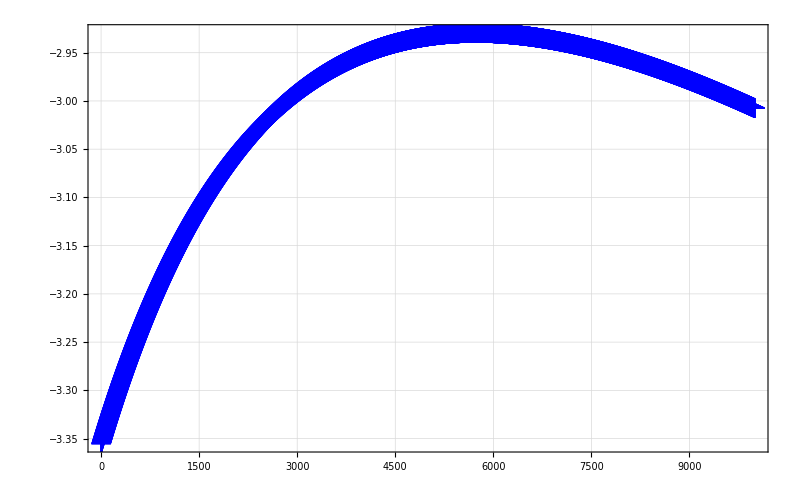

```mathematica
Texplot[steps, ϕlist[[;;, 1]], 800, "\\text{Discretisation step}", "x~\\text{coordinate}"]
```

```mathematica
(*Order of the error in the constraint equations*)
```

```mathematica
e1table= Table[Max[Abs[cη@@Join[ϕlist[[ii]], rinter[[ii]]]]], {ii, Length[ϕlist]}];
```

```mathematica
Max[e1table]
```

9.75433×10^-11

```mathematica
paperval = {e1-> −3.3553981637732204646, e2-> 0.5425359168641715099, e3-> +1.7110227662077546889, x-> +2.9313331749199504570, y-> +4.0768903590846968732, z-> +6.0451905744644536057};
```

```mathematica
paperval = ambrule;
```

```mathematica
cη@@Join[vars/.paperval, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
(*Visualisation*)
```

```mathematica
B1list = Table[B1/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B2list = Table[B2/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B3list = Table[B3/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
```

```mathematica
centerlist = (B1list+B2list+B3list+ϕlist[[;;,4;;]])/4;
```

```mathematica
sol = Inner[Rule, vars, ϕlist[[1]], List];
```

```mathematica
plotCDPR[sol_]:=Module[{cdpr, cables, base, tet, winches, fixtures, axis},
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[1]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
axis=Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{A1,{3,0,0}},0.075]]}],Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{A1,{0,3,0}},0.075]]}],Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{A1,{0,0,3}},0.075]]}]];
cdpr = Show[cables, base, tet, winches, fixtures, axis, Axes->False,AxesOrigin->Automatic, AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}];
Return[cdpr];
]
```

```mathematica
plotCDPR[ϕrule[[1]]];
```

```mathematica
ϕrule = Table[Inner[Rule, vars, ϕlist[[ii]], List],{ii, Length[ϕlist]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist], 1}
]
```

```mathematica
tic[]
tempϕ = test;
ϕlist = {tempϕ};
For[i=2,i≤Length[rinter], i = i+15, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.02552 seconds.

CPU time consumed: 0.025502 seconds.

Verifying if the solutions tracked also admit positive tensions in the entire path. Following from Eq.(5) from M. Carricatos paper, we can form equations in the tensions as,

```mathematica
Τ = {τ1/ρ1, τ2/ρ2, τ3/ρ3, f};
τeqns = Mo.Τ/.numdata;
```

```mathematica
τ3inf = Solve[τeqns[[-3]]==0, τ3][[1]]//FullSimplify;
τ2inf = Solve[τeqns[[5]]==0, τ2][[1]]//FullSimplify;
τ1inf = Solve[(τeqns[[1]]/.τ3inf/.τ2inf)==0, τ1][[1]]//FullSimplify;
```

Here the force f is nothing but the weight of the moving platform of the CDPR, which would be mg

```mathematica
τlist = Flatten[{τ1inf, τ2inf, τ3inf}];
```

```mathematica
soltable = Table[Inner[Rule, {e1, e2, e3, x, y, z}, roots[[i]], List], {i, Length[roots]}];
```

```mathematica
negroots = {{−2.6616890629909497781,+0.4160373487571940226,+0.9655548628886102991,
+2.5977352480361477511,+3.8457865212868645040,−4.8661048045758031135}, {−2.5291311336353393166,+7.3670838551717188775,−3.0436947470784328872,
+4.3757198849572551337,+5.8522722689950264632,−4.0010370837572794347}, {−0.3252555841337169146,−0.8891989606461705137,−1.6130562813850683595,
+2.5760653793782856615,+4.3924466541541392403,−6.7527508537785241857}, {+0.6844447542486557310,−0.0996112288836193264,+0.5262976928395059876,
+2.8401864910572365897,+4.8133317875987522652,−4.4534720523569757781}};
```

```mathematica
negsoltable = Table[Inner[Rule, {e1, e2, e3, x, y, z}, negroots[[i]], List], {i, Length[negroots]}];
```

```mathematica
Table[τlist/.f->10/.soltable[[i]], {i, Length[soltable]}]//MatrixForm
```

(τ1→6.84325821814767147 | τ2→3.05134203607141106 | τ3→6.14353554524815555
τ1→5.26131355440056486 | τ2→5.114315325379808 | τ3→5.81264928557445962
τ1→6.7588649712726997 | τ2→2.50870724809308364 | τ3→4.86403809930493806
τ1→5.4590170671983258 | τ2→3.25455992121066743 | τ3→5.49955494250124728
τ1→2.8863842770157147 | τ2→7.86815848220845137 | τ3→9.12427213576081342
τ1→5.8992443161536289 | τ2→7.82787558674089412 | τ3→9.56378969659922168)

```mathematica
Table[τlist/.f->10/.negsoltable[[i]], {i, Length[negsoltable]}]//MatrixForm
```

(τ1→-5.70723116276633533 | τ2→-4.84838310504563858 | τ3→-5.59091934069401378
τ1→-1.4042602559240844 | τ2→-9.30100384230561146 | τ3→-9.83319548298268639
τ1→-4.6090834876963252 | τ2→-4.11534637363950276 | τ3→-5.65301977282932134
τ1→-6.0096520004602357 | τ2→-7.60755504738133283 | τ3→-9.5298985934049558)

Now we have a method to compute the tensions given the task-space coordinates

```mathematica
tracktable = Table[Inner[Rule, {e1, e2, e3, x, y, z}, ϕlist[[i]], List], {i, Length[ϕlist]}];
```

```mathematica
tracktensions = Table[{τ1, τ2, τ3}/.τlist/.f->10/.tracktable[[i]], {i, Length[tracktable]}];
```

```mathematica
Min[tracktensions]>0
```

True

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=4; (*Magnification in axis and axis labesl*)
fontsize=40; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

Therefore all the roots tracked by the tracker are always physically feasible also

```mathematica
plot = ListPlot[{tracktensions[[;;, 1]], tracktensions[[;;, 2]],tracktensions[[;;, 3]]}, PlotMarkers->{"OpenMarkers", 10}, Joined->True, PlotRange->All, BaseStyle->{FontFamily->"Latin Modern Roman"}, Frame->True,FrameStyle->{Directive[Black,40],Directive[Black,40]}, GridLines->Automatic,PlotStyle->{Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]},FrameLabel->{MaTeX[ToString["\\text{"<>"Discretisation step"<>"}"],Magnification->3],MaTeX[ToString["\\text{Cable tensions}"],Magnification->3]},Joined->True, ImageSize->800, PlotLegends->{Placed[{MaTeX["\\tau_1", Magnification->3],MaTeX["\\tau_2", Magnification->3],MaTeX["\\tau_3", Magnification->3]},{Top, {0.5, 0.9}}]}, DataRange->{1, 1000}, ImageSize->800]
```

-Graphics-

Now we use the SEI algo to find the singular location of the CDPR, which should be done in CPP. 
To solve the SEI problem, we need IK and path param of the CDPR

```mathematica
parampath
```

{15/2+(5 α)/2,10+α,19/2-(3 α)/2}

Converting the roots into x, y, z, c1, c2, c3 form

```mathematica
rootsn = Join[roots[[;;,4;;]],roots[[;;,;;3]], 2];
```

```mathematica
rootsn//MatrixForm
```

(1.680460369602039094 | 3.574304753604949341 | 5.560547575098885676 | -4.222021637621852537 | -5.904163286951521036 | -0.47192841642603461
2.931333174919950457 | 4.076890359084696873 | 6.045190574464453606 | -3.355398163773220465 | 0.54253591686417151 | 1.711022766207754689
1.399260768351113312 | 3.279485251018208848 | 5.531283453882646946 | -1.165849928647269965 | -1.273125030159222373 | -1.006600278620949683
1.815931381103696648 | 4.302218951377045822 | 5.551637175521627389 | -0.548349869662383599 | -0.487718832794063759 | -1.21059601726598854
3.523134436600384322 | 5.532023636750048292 | 5.26267794130572783 | -0.504473758118947044 | 2.590309714688803771 | -1.24795509295964094
3.02409544832086876 | 4.730973851523787306 | 3.301921536759369036 | 0.543433219772396932 | -0.145505657428234931 | 0.569621999952391106)

For the root tracking using in the extended space we would need all the variables, which means we need an IKsolver

Otherway to solve this problem is to keep the problem within the task space itself, i.e., since we have the constraints and the Jacobian in qx and l, we can pose the problem in just within these variables

We are tracking the second branch from initsols in CPP

Converting the constraints and the Jacobian to CPP

```mathematica
CForm[Jn/.{ρ1->l1, ρ2->l2, ρ3->l3, e1->c1, e2->c2, e3->c3}//Simplify//Flatten]/.{Power->pow};
```

```mathematica
cJn@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]//MatrixForm;
```

```mathematica
CForm[η/.{ρ1->l1, ρ2->l2, ρ3->l3, e1->c1, e2->c2, e3->c3}//Simplify//Flatten]/.{Power->pow};
```

```mathematica
cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]//MatrixForm;
```

Tracking and visualising all the motion of all the branches

```mathematica
roots//Dimensions
```

{6,6}

```mathematica
(*tic[]
tempϕ = negroots[[4]];
ϕlist1 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist1, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist1[[ii]], List],{ii, Length[ϕlist1]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist1], 1}
]*)
```

#### Root - 1

```mathematica
rinitial = {15/2, 10, 19/2};
rfinal = {10,11,8};
rinter = Table[rinitial+ii*(rfinal-rinitial),{ii, 0, 1, 0.0001}];
```

```mathematica
tic[]
tempϕ = roots[[1]];
ϕlist1 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist1, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist1[[ii]], List],{ii, Length[ϕlist1]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist1], 1}
]
```

Actual time consumed: 3.36765 seconds.

CPU time consumed: 3.96159 seconds.

#### Root - 2

```mathematica
(*tic[]
tempϕ = roots[[2]];
ϕlist2 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist2, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist2[[ii]], List],{ii, Length[ϕlist2]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist2], 1}
]*)
```

#### Root - 3

```mathematica
(*tic[]
tempϕ = roots[[3]];
ϕlist3 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist3, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist3[[ii]], List],{ii, Length[ϕlist3]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist3], 1}
]*)
```

#### Root - 4

```mathematica
(*tic[]
tempϕ = roots[[4]];
ϕlist4 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist4, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist4[[ii]], List],{ii, Length[ϕlist4]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist4], 1}
]*)
```

#### Root - 5

```mathematica
(*tic[]
tempϕ = roots[[5]];
ϕlist5 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist5, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist5[[ii]], List],{ii, Length[ϕlist5]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist5], 1}
]*)
```

#### Root - 6

```mathematica
(*tic[]
tempϕ = roots[[6]];
ϕlist6 = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = NRTracking[rinter[[i]], tempϕ, cη, cJn];
AppendTo[ϕlist6, tempϕ];
]
toc[]

ϕrule = Table[Inner[Rule, vars, ϕlist6[[ii]], List],{ii, Length[ϕlist6]}];
Manipulate[
Show[plotCDPR[ϕrule[[u]]], Graphics3D[Table[{Red, Sphere[{x, y, z}/.ϕrule[[ii]], 0.1]},{ii, u}]]],
{u, 1, Length[ϕlist6], 1}
]*)
```

Give input with all the roots for the SEI

```mathematica
negrootsn = Join[negroots[[;;,4;;]],negroots[[;;,;;3]], 2];
```

```mathematica
allroots = Join[rootsn, negrootsn];
```

```mathematica
allroots//MatrixForm
```

(1.680460369602039094 | 3.574304753604949341 | 5.560547575098885676 | -4.222021637621852537 | -5.904163286951521036 | -0.47192841642603461
2.931333174919950457 | 4.076890359084696873 | 6.045190574464453606 | -3.355398163773220465 | 0.54253591686417151 | 1.711022766207754689
1.399260768351113312 | 3.279485251018208848 | 5.531283453882646946 | -1.165849928647269965 | -1.273125030159222373 | -1.006600278620949683
1.815931381103696648 | 4.302218951377045822 | 5.551637175521627389 | -0.548349869662383599 | -0.487718832794063759 | -1.21059601726598854
3.523134436600384322 | 5.532023636750048292 | 5.26267794130572783 | -0.504473758118947044 | 2.590309714688803771 | -1.24795509295964094
3.02409544832086876 | 4.730973851523787306 | 3.301921536759369036 | 0.543433219772396932 | -0.145505657428234931 | 0.569621999952391106
2.597735248036147751 | 3.845786521286864504 | -4.866104804575803114 | -2.661689062990949778 | 0.416037348757194023 | 0.965554862888610299
4.375719884957255134 | 5.852272268995026463 | -4.001037083757279435 | -2.529131133635339317 | 7.367083855171718878 | -3.043694747078432887
2.576065379378285662 | 4.39244665415413924 | -6.752750853778524186 | -0.325255584133716915 | -0.889198960646170514 | -1.61305628138506836
2.84018649105723659 | 4.813331787598752265 | -4.453472052356975778 | 0.684444754248655731 | -0.099611228883619326 | 0.526297692839505988)

```mathematica
allroots//Dimensions
```

{10,6}

```mathematica
sr = 1;
Table[Norm[allroots[[sr]]-allroots[[i]]],{i, Length[allroots]}]//MatrixForm
```

(0
7.00916518841003018
5.5892238275518348
6.627794163800071
9.68995812560776337
8.0747232255784882
12.412739721622386
17.0142094165446934
13.9544117889463253
12.7249139164639838)

```mathematica
Table[Det[cJn@@Join[rinter[[6]], allroots[[i]]]], {i, Length[allroots]}]
```

{-4.82042×10^29,-1.8084×10^30,-7.01348×10^28,-7.74481×10^29,-2.06755×10^30,-7.906×10^29,4.88091×10^30,1.09411×10^30,1.05001×10^31,3.4877×10^30}

```mathematica
allroots1 = Table[NRTracking[rinter[[6]], allroots[[i]], cη, cJn],{i, Length[allroots]}]
allroots1//MatrixForm
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{464599.,-309582.,-1.17171×10^6,2.57261×10^7,-3.35921×10^6,3.05752×10^7},{-161074.,59367.2,385158.,-1.30846×10^7,-1.00324×10^6,1.49024×10^6},{57216.7,«4»,1.78254×10^6},{«1»},{2.91208×10^12,-4.08833×10^12,1.28117×10^12,6.47846×10^13,1.04661×10^14,-1.84475×10^13},{-3.33979×10^12,-1.22201×10^12,1.02247×10^13,-8.51145×10^13,5.43036×10^13,-9.26297×10^13}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-7.07854×10^9,-5.69442×10^9,-4.71976×10^9,-5.89004×10^11,5.97549×10^11,-2.84588×10^11},{-2.12971×10^8,-1.37951×10^8,-1.32904×10^8,-2.09054×10^10,-2.62769×10^9,-2.95861×10^8},{2.80944×10^8,«4»,-«22»},{«1»},{-7.48687×10^19,-5.48667×10^19,-4.68207×10^19,-2.20607×10^21,4.86453×10^21,7.43523×10^20},{-3.36215×10^19,-6.48671×10^19,6.82074×10^18,2.32998×10^21,7.90635×10^21,3.68723×10^21}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-4.32431×10^10,1.70989×10^10,2.43418×10^10,2.15959×10^11,1.2172×10^13,-1.42287×10^13},{1.77768×10^8,1.00845×10^8,-2.9759×10^8,-4.87048×10^11,-1.08186×10^10,4.75255×10^10},{«1»},{«23»,-«22»,«3»,0.},{1.27168×10^22,-3.74511×10^20,-5.03246×10^21,-1.44324×10^24,-1.77016×10^24,1.52285×10^24},{5.04075×10^21,-7.65615×10^21,-1.0683×10^22,-1.14877×10^24,-1.75143×10^24,1.24948×10^24}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{-0.505059,2.59112,-1.24845,3.52378,5.53338,5.26275},{-0.325081,-0.889164,-1.61325,2.57653,4.39395,-6.75311},{6.93947×10^33,-1.49205×10^35,8.62204×10^34,-2.63084×10^6,2.14575×10^6,-4.83533×10^6},{3.53137×10^42,4.00076×10^42,1.75652×10^43,-9.33186×10^12,-1.88002×10^13,1.08433×10^14},{-0.325081,-0.889164,-1.61325,2.57653,4.39395,-6.75311},{-0.549175,-0.489204,-1.21039,1.81549,4.30097,5.55207},{-4.35961×10^23,-3.98273×10^23,3.07452×10^23,1.67499,4.55402,-4.43808},{-2.52942,7.36667,-3.0433,4.37639,5.85372,-4.00094},{0.54338,-0.145426,0.569574,3.02445,4.73219,3.30233},{-3.37104×10^11,7.69763×10^11,-3.86428×10^11,4.46863,5.94348,-4.02501}}

(-0.505059 | 2.59112 | -1.24845 | 3.52378 | 5.53338 | 5.26275
-0.325081 | -0.889164 | -1.61325 | 2.57653 | 4.39395 | -6.75311
6.93947×10^33 | -1.49205×10^35 | 8.62204×10^34 | -2.63084×10^6 | 2.14575×10^6 | -4.83533×10^6
3.53137×10^42 | 4.00076×10^42 | 1.75652×10^43 | -9.33186×10^12 | -1.88002×10^13 | 1.08433×10^14
-0.325081 | -0.889164 | -1.61325 | 2.57653 | 4.39395 | -6.75311
-0.549175 | -0.489204 | -1.21039 | 1.81549 | 4.30097 | 5.55207
-4.35961×10^23 | -3.98273×10^23 | 3.07452×10^23 | 1.67499 | 4.55402 | -4.43808
-2.52942 | 7.36667 | -3.0433 | 4.37639 | 5.85372 | -4.00094
0.54338 | -0.145426 | 0.569574 | 3.02445 | 4.73219 | 3.30233
-3.37104×10^11 | 7.69763×10^11 | -3.86428×10^11 | 4.46863 | 5.94348 | -4.02501)

```mathematica
sr = 1;
Table[Norm[allroots1[[sr]]-allroots1[[i]]],{i, Length[allroots]}]//MatrixForm
```

(0.
12.6037
1.72466×10^35
1.83579×10^43
12.6037
3.74334
6.65741×10^23
10.8061
4.07769
9.24933×10^11)

I think that all of these problems are due to the ill posed constraint and Jacobian equations. Pose them properly as in the case of SRSPM and then try again. 
Also could this be because the system is underactuated and hence not enough equations in some way?